# Arm state visualization

## Import

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_16__15_03_16/"; (* Mv2 *)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_12__19_20_02/"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_13__13_03_05/"; (* Mv1 *)*)
SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]];
data = all[[2;;-2]];
numVars=Dimensions[varNames]
numData=Length[data]

fitXml = Import["GA_Progress.xml"];
fitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
fitness=ToExpression[fitness];
```

{116}

1800

## Fitness

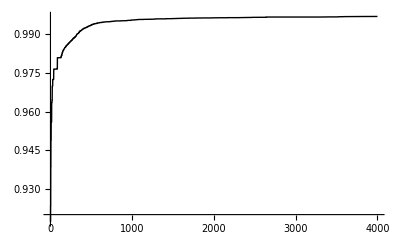

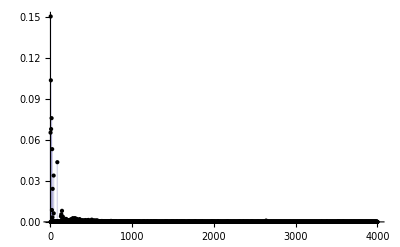

```mathematica
fitDiff=10*Differences[fitness];
fitDiff =PadRight[fitDiff,Length[fitness],Last[fitDiff]];
fitP =ListLinePlot[fitness,PlotStyle->Black,PlotRange->All,ImageSize->400]
fitDiffP = ListPlot[fitDiff,PlotStyle->Black,Filling->Axis,PlotRange->All,ImageSize->400]
```

## Config

```mathematica
dt = 0.001;
trial = 1;
leadIn = 0.3;
leadOut = 0.3;
moveDuration = 0.3;
bestFitDelay = -0.015 / dt;
plotDuration = (moveDuration+leadOut/3) / dt;

trialDuration = leadIn+moveDuration+leadOut;
frontLead =0.1;
backLead = 0.2;
t0=(leadIn-frontLead+ (trial*trialDuration))/dt
tn = t0 +(moveDuration+backLead)/dt
time = Range[tn-t0]*dt;
padds={{20,40},{20,20}};
plotOptions = {PlotJoined->True, PlotRange->All, ImagePadding->padds};
graphicsWidth = 600;
```

1100.

1600.

## Functions

```mathematica
NtoI[name_]:=Position[varNames, name][[1,1]];
NtoD[name_, delay_:0]:=Table[data[[i,NtoI[name]]],{i,t0+delay,tn-1+delay}];
TimePlot[name_, options_, delay_:0] := ListLinePlot[Transpose[{time,NtoD[name, delay]}], Join[plotOptions,options]];
TimePlotD[data_, options_] := ListLinePlot[Transpose[{time,data}], Join[plotOptions,options]];
```

## Draw arm kinematics

```mathematica
(* Joint trajectories *)
angleElb =TimePlot["angleElbow",{PlotStyle->{Black}, AxesLabel->{"time","angle"}}];
desAngleElb = TimePlot["desElbow",{PlotStyle->{Black,Dashed}, AxesLabel->{"time","angle"}}, bestFitDelay];
comAngleElb = TimePlot["comElbow",{PlotStyle->{Gray}, AxesLabel->{"time","angle"}}];
angleShd= TimePlot["angleShoulder",{PlotStyle->{Black}}];
desAngleShd = TimePlot["desShoulder",{PlotStyle->{Black,Dashed}, AxesLabel->{"time","angle"}}, bestFitDelay];
comAngleShd = TimePlot["comShoulder",{PlotStyle->{Gray}, AxesLabel->{"time","angle"}}];
elbow = Show[angleElb, desAngleElb, comAngleElb];
shoulder = Show[angleShd, desAngleShd, comAngleShd];
angles = Show[angleElb,desAngleElb, angleShd];

(* Calculate derivatives *)
accScale = 10;

velElb= TimePlot["velocityElbow",{PlotStyle->{Black}, AxesLabel->{"time","velocity"}}];
desVelElbD = Differences[NtoD["desElbow", bestFitDelay]]/dt;
desVelElbD = PadRight[desVelElbD,Length[time],Last[desVelElbD]];
desVelElb = TimePlotD[desVelElbD,{PlotStyle->{Black,Dashed}}];
desAccElbD = Differences[desVelElbD]/dt/accScale;
desAccElbD = PadRight[desAccElbD,Length[time],Last[desAccElbD]];
desAccElbD = MovingAverage[desAccElbD,3];
desAccElbD = PadRight[desAccElbD,Length[time],Last[desAccElbD]];
desAccElb = TimePlotD[desAccElbD,{PlotStyle->{Gray}}];

velShd= TimePlot["velocityShoulder",{PlotStyle->{Black}}];
desVelShdD = Differences[NtoD["desShoulder", bestFitDelay]]/dt;
desVelShdD = Append[desVelShdD,desVelShdD[[Length[desVelShdD]]]];
desVelShd = TimePlotD[desVelShdD,{PlotStyle->{Black,Dashed}}];
desAccShdD = Differences[desVelShdD]/dt/accScale;
desAccShdD = PadRight[desAccShdD,Length[time],Last[desAccShdD]];
desAccShdD = MovingAverage[desAccShdD,3];
desAccShdD = PadRight[desAccShdD,Length[time],Last[desAccShdD]];
desAccShd = TimePlotD[desAccShdD,{PlotStyle->{Gray}}];

velsElb = Show[velElb, desVelElb, desAccElb];
velsShd = Show[velShd, desVelShd, desAccShd];
vels = Show[velElb,velShd];

(* Forces applied at joints, total is more or less acceleration *)
itElbD = -NtoD["interactionElbow"] - NtoD["coriolisElbow"];
totalElbD = NtoD["torqueElbow"]+itElbD;
totalElb = TimePlotD[totalElbD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, AxesLabel->{"time","forceElb"}}];
trqElb= TimePlot["torqueElbow",{PlotStyle->Black}];
itElb = TimePlotD[itElbD,{PlotStyle->{Black,Dashed}}];
trqsElb = Show[totalElb,trqElb, itElb];

itShdD = -NtoD["interactionShoulder"] - NtoD["coriolisShoulder"];
totalShdD = NtoD["torqueShoulder"]+itShdD;
totalShd = TimePlotD[totalShdD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent},AxesLabel->{"time","forceShd"}}];
trqShd= TimePlot["torqueShoulder",{PlotStyle->Black}];
itShd = TimePlotD[itShdD,{PlotStyle->{Black,Dashed}}];
trqsShd = Show[totalShd,trqShd, itShd];

(* Effector space trajectories, i.e. cartesian position *)
xPos = TimePlot["x",{PlotStyle->{Black}, AxesLabel->{"time","x,y"}}];
desX = TimePlot["desX",{PlotStyle->{Black, Dashed}, AxesLabel->{"time","x,y"}}, bestFitDelay];
comX = TimePlot["comX",{PlotStyle->{Gray}, AxesLabel->{"time","x,y"}}];
yPos = TimePlot["y",{PlotStyle->{Black}}];
desY = TimePlot["desY",{PlotStyle->{Black, Dashed}, AxesLabel->{"time","x,y"}}, bestFitDelay];
comY = TimePlot["comY",{PlotStyle->{Gray}, AxesLabel->{"time","x,y"}}];
pos = Show[xPos,yPos, desX, desY];
posX = Show[xPos, desX, comX];
posY = Show[yPos, desY, comY];

(* XY plot *)
x = NtoD["x"];
y = NtoD["y"];
positions=Transpose[{x,y}];
cartesianPos=ListLinePlot[positions,plotOptions,PlotStyle->Black,AxesOrigin->{Min[x],Min[y]}, AxesLabel->{"x","y"}];
startPos = Graphics[{PointSize[Large],Point[First[positions]]}];
desX = NtoD["desX", bestFitDelay];
desY = NtoD["desY", bestFitDelay];
desPos = Transpose[{desX,desY}];
desCartPos = ListLinePlot[desPos,plotOptions,PlotStyle->{Black,Dashed},AxesOrigin->{Min[x],Min[y]}, AxesLabel->{"x","y"}];
xyPos = Show[cartesianPos,desCartPos,startPos];

(* Calculate tangential velocity *)
vels= Map[Norm,Differences[positions]]/dt;
vels=PadRight[vels,Length[time],Last[vels]];
tangVel=TimePlotD[vels,{PlotStyle->{Black},AxesLabel->{"time","vel"}}];
desVels = Map[Norm,Differences[desPos]]/dt;
desVels = PadRight[desVels,Length[time],Last[desVels]];
tangDesVel = TimePlotD[desVels,{PlotStyle->{Black,Dashed},AxesLabel->{"time","vel"}}];
cartVels = Show[tangVel,tangDesVel]; 

(*(gg=GraphicsGrid[{{pos,angles,vels},{accs,trqsElb, trqsShd}}, ImageSize->{1200}]*)
armPlots=GraphicsGrid[{{xyPos, cartVels},{posX, posY},{elbow, shoulder}, {velsElb,velsShd}, {trqsElb,trqsShd}}, ImageSize->graphicsWidth];

(*Export["export.pdf", gg, "pdf"]*)
```

## Reflex plots

```mathematica
(* Input: desired contraction modified by intersegmental input *)
desContrElbAgP =  TimePlot["reflexElbDesContractionAg",{PlotStyle->Black, AxesLabel->{"time","DesContr"}}];
desContrElbAnP =  TimePlot["reflexElbDesContractionAn",{PlotStyle->{Black,Dashed}}];
comContrElbAgP =  TimePlot["reflexElbComContractionAg",{PlotStyle->{Gray}}];
comContrElbAnP =  TimePlot["reflexElbComContractionAn",{PlotStyle->{Gray,Dashed}}];
desContrElbPlot =Show[desContrElbAgP,desContrElbAnP,comContrElbAgP,comContrElbAnP];

desContrShdAgP =  TimePlot["reflexShdDesContractionAg",{PlotStyle->Black, AxesLabel->{"time","DesContr"}}];
desContrShdAnP =  TimePlot["reflexShdDesContractionAn",{PlotStyle->{Black,Dashed}}];
comContrShdAgP =  TimePlot["reflexShdComContractionAg",{PlotStyle->{Gray}}];
comContrShdAnP =  TimePlot["reflexShdComContractionAn",{PlotStyle->{Gray,Dashed}}];
desContrShdPlot =Show[desContrShdAgP,desContrShdAnP,comContrShdAgP,comContrShdAnP];

(* Overall output: alpha MN *)
aMNElbAgP =  TimePlot["reflexElbMNAg",{PlotStyle->Black, AxesLabel->{"time","aMN"}}];
aMNElbAnP =  TimePlot["reflexElbMNAn",{PlotStyle->{Black,Dashed}}];
aMNElbPlot =Show[aMNElbAgP,aMNElbAnP ];

aMNShdAgP =  TimePlot["reflexShdMNAg",{PlotStyle->Black, AxesLabel->{"time","aMN"}}];
aMNShdAnP =  TimePlot["reflexShdMNAn",{PlotStyle->{Black,Dashed}}];
aMNShdPlot =Show[aMNShdAgP,aMNShdAnP ];

(* Open loop activation *)
oplpElbAgP =  TimePlot["reflexElbOpenLoopAg",{PlotStyle->Black, AxesLabel->{"time","openLoop"}}];
oplpElbAnP =  TimePlot["reflexElbOpenLoopAn",{PlotStyle->{Black,Dashed}}];
oplpElbPlot=Show[oplpElbAgP,oplpElbAnP ];

oplpShdAgP =  TimePlot["reflexShdOpenLoopAg",{PlotStyle->Black, AxesLabel->{"time","openLoop"}}];
oplpShdAnP =  TimePlot["reflexShdOpenLoopAn",{PlotStyle->{Black,Dashed}}];
oplpShdPlot=Show[oplpShdAgP,oplpShdAnP ];

(* Spindles *)
spElbAgP =  TimePlot["reflexElbSpResAg",{PlotStyle->Black, AxesLabel->{"time","spindle"}}];
spElbAnP =  TimePlot["reflexElbSpResAn",{PlotStyle->{Black,Dashed}}];
spindleElbPlot =Show[spElbAgP,spElbAnP ];

spShdAgP =  TimePlot["reflexShdSpResAg",{PlotStyle->Black, AxesLabel->{"time","spindle"}}];
spShdAnP =  TimePlot["reflexShdSpResAn",{PlotStyle->{Black,Dashed}}];
spindleShdPlot =Show[spShdAgP,spShdAnP ];

(* Spindles components*)
spElbAgPosP =  TimePlot["reflexElbPosResAg",{PlotStyle->Black, AxesLabel->{"time","spCmpAg"}}];
spElbAgVelP =  TimePlot["reflexElbVelResAg",{PlotStyle->{Black,Dashed}}];
spElbAgDmpP =  TimePlot["reflexElbDmpResAg",{PlotStyle->{Black,Dotted}}];
spShdAgPosP =  TimePlot["reflexShdPosResAg",{PlotStyle->Black}];
spShdAgVelP =  TimePlot["reflexShdVelResAg",{PlotStyle->{Black,Dashed}}];
spShdAgDmpP =  TimePlot["reflexShdDmpResAg",{PlotStyle->{Black,Dotted}}];
spCmpElbAgPlot =Show[spElbAgPosP,spElbAgVelP,spElbAgDmpP];
spCmpShdAgPlot =Show[spShdAgPosP,spShdAgVelP,spShdAgDmpP];

spElbAnPosP =  TimePlot["reflexElbPosResAn",{PlotStyle->Black, AxesLabel->{"time","spCmpAn"}}];
spElbAnVelP =  TimePlot["reflexElbVelResAn",{PlotStyle->{Black,Dashed}}];spElbAnDmpP =  TimePlot["reflexElbDmpResAn",{PlotStyle->{Black,Dotted}}];
spShdAnPosP =  TimePlot["reflexShdPosResAn",{PlotStyle->Black}];
spShdAnVelP =  TimePlot["reflexShdVelResAn",{PlotStyle->{Black,Dashed}}];spShdAnDmpP =  TimePlot["reflexShdDmpResAn",{PlotStyle->{Black,Dotted}}];
spCmpElbAnPlot =Show[spElbAnPosP,spElbAnVelP,spElbAnDmpP];
spCmpShdAnPlot =Show[spShdAnPosP,spShdAnVelP,spShdAnDmpP];

reflexPlots = GraphicsGrid[{{desContrElbPlot, desContrShdPlot},{aMNElbPlot, aMNShdPlot}, {oplpElbPlot,oplpShdPlot},{spindleElbPlot,spindleShdPlot},{spCmpElbAgPlot,spCmpShdAgPlot},{spCmpElbAnPlot,spCmpShdAnPlot}}, ImageSize->graphicsWidth];
```

## Muscle Plots

```mathematica
elbAgActP = TimePlot["ElbowFlexorAct",{PlotStyle->{Black},AxesLabel->{"time","Act"}}];
elbAnActP = TimePlot["ElbowExtensorAct", {PlotStyle->{Black,Dashed}}];
elbAct = Show[elbAgActP, elbAnActP];

shdAgActP = TimePlot["ShoulderFlexorAct",{PlotStyle->{Black}}];
shdAnActP = TimePlot["ShoulderExtensorAct", {PlotStyle->{Black,Dashed}}];
shdAct = Show[shdAgActP, shdAnActP];


elbAgFrcP = TimePlot["ElbowFlexorForce",{PlotStyle->{Black},AxesLabel->{"time","Force"}}];
elbAnFrcP = TimePlot["ElbowExtensorForce", {PlotStyle->{Black,Dashed}}];
elbFrcTotal = Show[elbAgFrcP, elbAnFrcP];

shdAgFrcP = TimePlot["ShoulderFlexorForce",{PlotStyle->{Black}}];
shdAnFrcP = TimePlot["ShoulderExtensorForce", {PlotStyle->{Black,Dashed}}];
shdFrcTotal = Show[shdAgFrcP, shdAnFrcP];


elbAgLengthP = TimePlot["ElbowFlexorLengthNorm",{PlotStyle->{Black},AxesLabel->{"time","Length"}}];
elbAnLengthP = TimePlot["ElbowExtensorLengthNorm", {PlotStyle->{Black,Dashed}}];
elbAgVelP = TimePlot["ElbowFlexorVelocityNorm",{PlotStyle->{Gray}}];
elbAnVelP = TimePlot["ElbowExtensorVelocityNorm", {PlotStyle->{Gray,Dashed}}];
elbKin = Show[elbAgLengthP,elbAnLengthP,elbAgVelP,elbAnVelP];

shdAgLengthP = TimePlot["ShoulderFlexorLengthNorm",{PlotStyle->{Black}}];
shdAnLengthP = TimePlot["ShoulderExtensorLengthNorm", {PlotStyle->{Black,Dashed}}];
shdAgVelP = TimePlot["ShoulderFlexorVelocityNorm",{PlotStyle->{Gray}}];
shdAnVelP = TimePlot["ShoulderExtensorVelocityNorm", {PlotStyle->{Gray,Dashed}}];
shdKin = Show[shdAgLengthP,shdAnLengthP,shdAgVelP,shdAnVelP];

elbAgActFrcP = TimePlot["ElbowFlexorFrcAct", {PlotStyle->{Black},AxesLabel->{"time","FrcCmp"}}];
elbAnActFrcP = TimePlot["ElbowExtensorFrcAct", {PlotStyle->{Black,Dashed}}];
elbAgVelFrcP = TimePlot["ElbowFlexorFrcVel", {PlotStyle->{Gray},AxesLabel->{"time","FrcCmp"}}];
elbAnVelFrcP = TimePlot["ElbowExtensorFrcVel", {PlotStyle->{Gray,Dashed}}];
elbAgPsvFrcP = TimePlot["ElbowFlexorFrcPsv", {PlotStyle->{LightGray},AxesLabel->{"time","FrcCmp"}}];
elbAnPsvFrcP = TimePlot["ElbowExtensorFrcPsv", {PlotStyle->{LightGray,Dashed}}];
elbFrc = Show[elbAgActFrcP, elbAnActFrcP,elbAgVelFrcP,elbAnVelFrcP,elbAgPsvFrcP,elbAnPsvFrcP];

shdAgActFrcP = TimePlot["ShoulderFlexorFrcAct", {PlotStyle->{Black}}];
shdAnActFrcP = TimePlot["ShoulderExtensorFrcAct", {PlotStyle->{Black,Dashed}}];
shdAgVelFrcP = TimePlot["ShoulderFlexorFrcVel", {PlotStyle->{Gray}}];
shdAnVelFrcP = TimePlot["ShoulderExtensorFrcVel", {PlotStyle->{Gray,Dashed}}];
shdAgPsvFrcP = TimePlot["ShoulderFlexorFrcPsv", {PlotStyle->{LightGray}}];
shdAnPsvFrcP = TimePlot["ShoulderExtensorFrcPsv", {PlotStyle->{LightGray,Dashed}}];
shdFrc = Show[shdAgActFrcP, shdAnActFrcP,shdAgVelFrcP,shdAnVelFrcP,shdAgPsvFrcP,shdAnPsvFrcP];


elbAgMaP = TimePlot["ElbowFlexorMomentArm",{PlotStyle->{Black},AxesLabel->{"time","MA"}}];
elbAnMaP = TimePlot["ElbowExtensorMomentArm", {PlotStyle->{Black,Dashed}}];
elbAgTorqueP = TimePlot["ElbowFlexorTorque",{PlotStyle->{Black},AxesLabel->{"time","Torque"}}];
elbAnTorqueP = TimePlot["ElbowExtensorTorque", {PlotStyle->{Black,Dashed}}];
elbTrq = Show[elbAgTorqueP,elbAnTorqueP];
elbMa = Show[elbAgMaP, elbAnMaP];

shdAgMaP = TimePlot["ShoulderFlexorMomentArm",{PlotStyle->{Black}}];
shdAnMaP = TimePlot["ShoulderExtensorMomentArm", {PlotStyle->{Black,Dashed}}];
shdAgTorqueP = TimePlot["ShoulderFlexorTorque",{PlotStyle->{Black}}];
shdAnTorqueP = TimePlot["ShoulderExtensorTorque", {PlotStyle->{Black,Dashed}}];
shdTrq = Show[shdAgTorqueP,shdAnTorqueP];
shdMa = Show[shdAgMaP, shdAnMaP];

musclePlots = GraphicsGrid[{{elbAct,shdAct},{elbFrcTotal,shdFrcTotal},{elbKin,shdKin},{elbFrc,shdFrc},{elbMa,shdMa},{elbTrq,shdTrq}},ImageSize->graphicsWidth];
```

## Phase Space plots

```mathematica
angleElbD = NtoD["angleElbow"];
velElbD = NtoD["velocityElbow"];
desAngleElbD = NtoD["desElbow",bestFitDelay];
actElbPhase = ListLinePlot[Transpose[{angleElbD,velElbD}],PlotStyle->Black,AxesLabel->{"angle","vel"},plotOptions];
desElbPhase = ListLinePlot[Transpose[{desAngleElbD,desVelElbD}],PlotStyle->{Black,Dashed},plotOptions];
elbPhase = Show[actElbPhase,desElbPhase];

angleShdD = NtoD["angleShoulder"];
velShdD = NtoD["velocityShoulder"];
desAngleShdD = NtoD["desShoulder",bestFitDelay];
actShdPhase = ListLinePlot[Transpose[{angleShdD,velShdD}],PlotStyle->Black,AxesLabel->{"angle","vel"}, plotOptions];
desShdPhase = ListLinePlot[Transpose[{desAngleShdD,desVelShdD}], PlotStyle->{Black,Dashed},plotOptions];
shdPhase = Show[actShdPhase, desShdPhase];

phSpacePlots =GraphicsRow[{elbPhase, shdPhase}, ImageSize->graphicsWidth];
```

## Output

Arm States

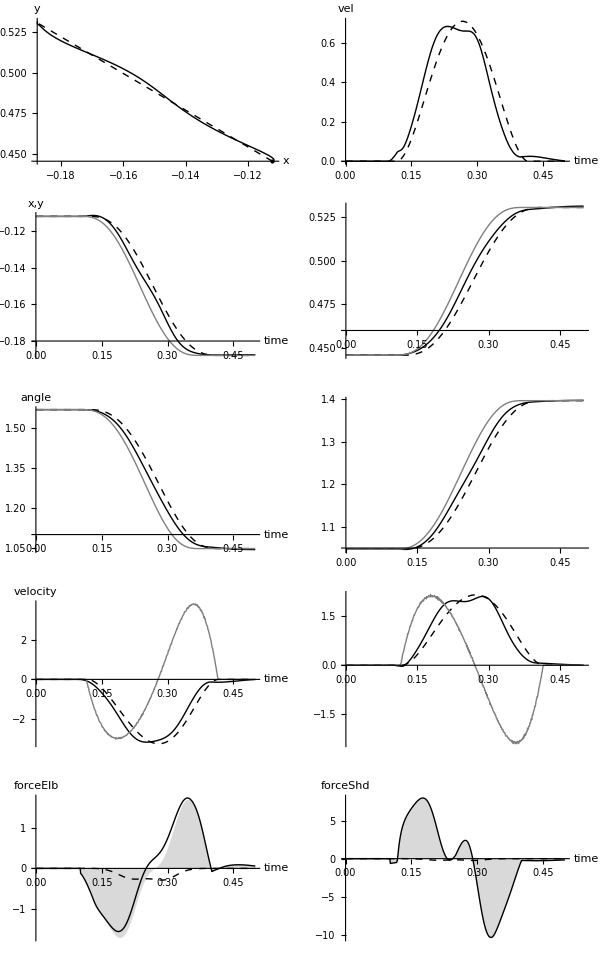

Reflex States

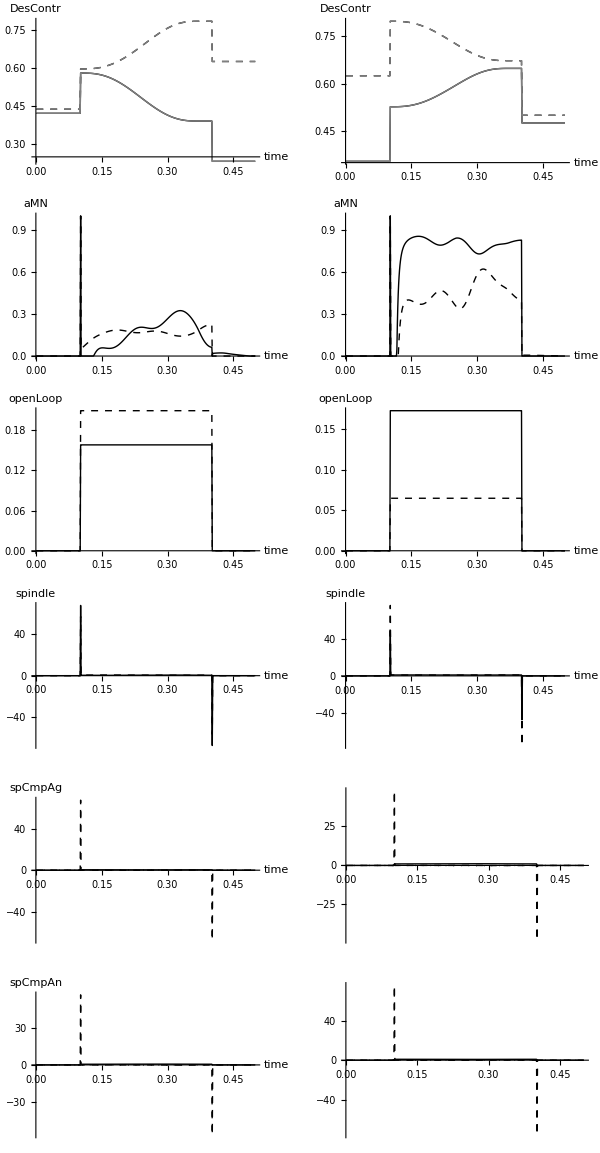

Muscle States

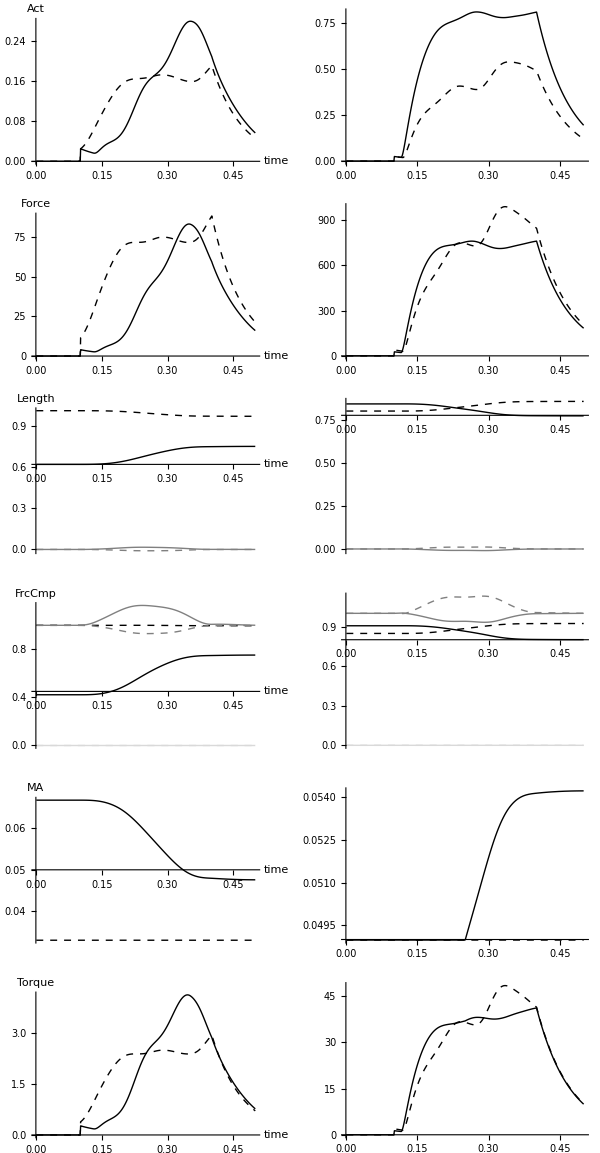

Phase space

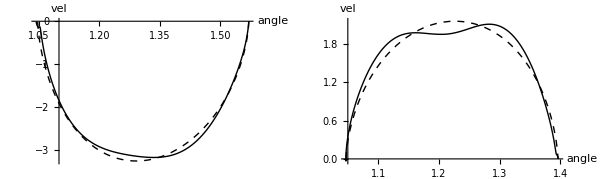

```mathematica
Print[Style["Arm States","Subtitle"]]
armPlots

Print[Style["Reflex States","Subtitle"]]
reflexPlots

Print[Style["Muscle States","Subtitle"]]
musclePlots

Print[Style["Phase space","Subtitle"]]
phSpacePlots
```